## Fredholm Integral Equation of the Second Kind with a Gaussian Kernel Eigenvalues and Eigenfunctions

```mathematica
nodd=21;
b=10;
a=1;
sol=NSolve[{1/b -x Tan[x a],(nodd-1) Pi/a<x<(nodd-1/2) Pi/a},x];
w=Part[x/.sol,1]
```

62.8334

```mathematica
λ=2b/(1+w^2 b^2)
```

0.0000506579

```mathematica
c=1/Sqrt[a+Sin[2 w a]/(2 w)];
φ[t_]:=c Cos[w t]
φ[t]
```

0.999987 Cos[62.8334 t]

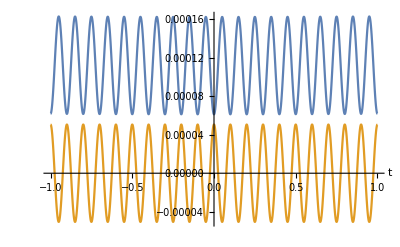

```mathematica
Plot[{NIntegrate[Exp[Abs[ti-tj]/b] φ[tj],{tj,-a,a}],λ φ[ti]},{ti,-a,a},AxesLabel->{"t",""}]
```

```mathematica
neven=5;
b=10;
a=1;
sol=NSolve[{1/b Tan[x a]+x,(neven-1/2) Pi/a<x<(neven) Pi/a},x];
w=Part[x/.sol,1]
```

14.1464

```mathematica
λ=2b/(1+w^2 b^2)
```

0.000999351

```mathematica
c=1/Sqrt[a+Sin[2 w a]/(2 w)];
φ[t_]:=c Cos[w t]
φ[t]
```

1.00033 Cos[14.1464 t]

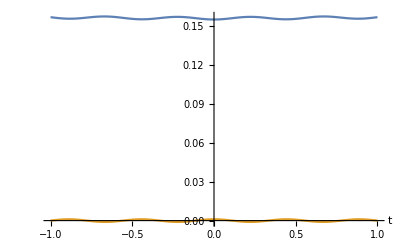

```mathematica
Plot[{NIntegrate[Exp[Abs[ti-tj]/b] φ[tj],{tj,-a,a}],λ φ[ti]},{ti,-a,a},AxesLabel->{"t",""}]
```